```mathematica
Quit
```

```mathematica
(* Created by Savvas Nesseris 2021 *)
```

```mathematica
(* A smooth model for transitions of the equation of state w(z) *)
wint[a_]:=α+β 1/2(1+((a-at)/da)/(√(1+((a-at)/da)^2)));
```

```mathematica
(* Match params for sqrt model so that the transition happens at a specified redshift etc *)
sol1={α->-(da (-1+(-1+at)/(√(1+(-1+at)^2/da^2) da)+(1-at/(√(1+at^2/da^2) da)) (1-Δw)))/((-1+at)/(√(1+(-1+at)^2/da^2))-at/(√(1+at^2/da^2))),β->(2 √(1+(-1+at)^2/da^2) √(1+at^2/da^2) da Δw)/(at (√(1+(-1+at)^2/da^2)-√(1+at^2/da^2))+√(1+at^2/da^2))};
wDE=wint[a]/.sol1;
```

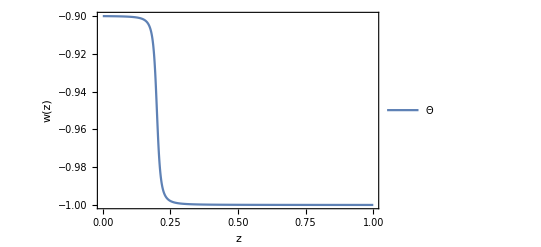

```mathematica
(* Example plot *)
Plot[wDE/.{da->0.01,Δw->0.1,at->1/(1+0.2)}/.a->1/(1+z)//Evaluate,{z,0,1},PlotRange->All,Frame->True,FrameLabel->{"z","w(z)"},PlotLegends->{"Θ","Sqrt"},FrameStyle->Black]
```

```mathematica
(* The DE density, and the equivalent potential and kinetic terms of a minimally couple scalar field, see Sahni and Starobinsky astro-ph/0610026 *)
Ωde[x_]:=((1-at+√((-1+at)^2+da^2))/(a-at+√((a-at)^2+da^2)))^((3 √((-1+at)^2+da^2) √(at^2+da^2) Δw)/(√(at^2+da^2)+at (√((-1+at)^2+da^2)-√(at^2+da^2)))) (((-1+at) at+da^2+√((-1+at)^2+da^2) √(at^2+da^2))/(-a at+at^2+da^2+√((a-at)^2+da^2) √(at^2+da^2)))^((3 at √((-1+at)^2+da^2) Δw)/(√(at^2+da^2)+at (√((-1+at)^2+da^2)-√(at^2+da^2))))/.a->1/x;
Vx=H[x]^2-x/6 D[H[x]^2,x]-1/2 om x^3;
phip2=ϵ(2/(3x)D[Log[H[x]],x]-(om x)/H[x]^2);
Vx1=Vx//FullSimplify;
phip21=phip2//FullSimplify;
H[x_]:=√(om x^3+(1-om)Ωde[x])
```

```mathematica
(* Parameters that correspond to quintessence and phantom fields *)
cosmoq={da->0.01,Δw->0.05,at->1/(1+0.2),om->.3,ϵ->1};
cosmop={da->0.01,Δw->-0.05,at->1/(1+0.2),om->.3,ϵ->-1};
```

```mathematica
(* Solve the ODEs in the two cases *)
solϕq=NDSolve[{ϕ'[x]==-√(phip21/.cosmoq),ϕ[100]==0},ϕ,{x,1,100}][[1]];
solϕp=NDSolve[{ϕ'[x]==-√(phip21/.cosmop),ϕ[100]==0},ϕ,{x,1,100}][[1]];
```

```mathematica
zϕq=Table[{ϕ[1+10^log10z]/.solϕq//Log10,Round[10^log10z//N,0.1]},{log10z,-1,1,0.25}]
zϕp=Table[{ϕ[1+10^log10z]/.solϕp//Log10,Round[10^log10z//N,0.1]},{log10z,-1,1,0.25}]
```

{{-1.70149,0.1},{-2.09772,0.2},{-2.66392,0.3},{-2.93905,0.6},{-3.23014,1.},{-3.57042,1.8},{-3.96173,3.2},{-4.39322,5.6},{-4.85354,10.}}

{{-1.70576,0.1},{-2.10351,0.2},{-2.67197,0.3},{-2.94849,0.6},{-3.24075,1.},{-3.5818,1.8},{-3.97347,3.2},{-4.40506,5.6},{-4.86542,10.}}

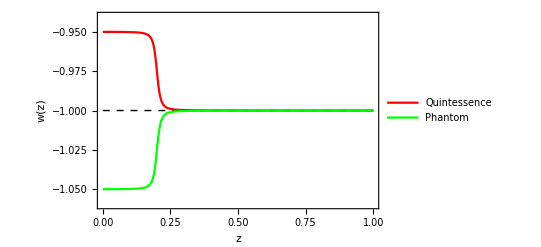
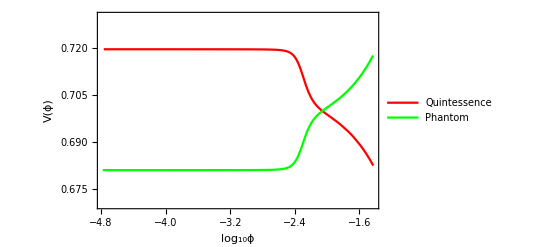

```mathematica
(* Make the plots *)
plots={Plot[{wDE/.cosmoq,wDE/.cosmop}/.a->1/(1+z)//Evaluate,{z,0,1},PlotRange->{All,{-1.06,-0.94}},Frame->True,FrameLabel->{"z","w(z)"},PlotLegends->Placed[{"Quintessence","Phantom"},Scaled[{0.8,0.85}]],FrameStyle->Black,ImageSize->400,PlotStyle->{Red,Green},BaseStyle->FontSize->13,Prolog->{Dashed,Line[{{0,-1},{2,-1}}]}],ParametricPlot[{{ϕ[x]/.solϕq//Log10,Vx1/.cosmoq},{ϕ[x]/.solϕp//Log10,Vx1/.cosmop}},{x,1,10},Frame->True,PlotRange->{All,{0.67,0.73}},AspectRatio->1/GoldenRatio,FrameStyle->Black,FrameLabel->{{"V(ϕ)",None},{"log_10ϕ","z"}},Axes->False,BaseStyle->FontSize->13,FrameTicks->{{Automatic,Automatic},{Automatic,zϕq}},PlotStyle->{Red,Green},PlotLegends->Placed[{"Quintessence","Phantom"},Scaled[{0.25,0.5}]],ImageSize->400]}
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["plot_transition_1.pdf",plots[[1]],ImageSize->700]
Export["plot_transition_2.pdF",plots[[2]],ImageSize->700]
```

plot_transition_1.pdf

plot_transition_2.pdF